# Plot Population Development

## Functions

```mathematica
<<PajaroLocoPublic`
<<Utilities`CleanSlate`
SetDirectory[NotebookDirectory[]]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
GraphMap2[{raw_,coordsRaw_,rawPop_,name_,pad_},maxTransitionsSize_,imageSize_,cityScaler_,cityScaler2_]:=Module[{coords,head,data,pops,popsVct,sizes,edgeshape,graph,coordSizePairs,points},
{coords,head,data,pops}={
coordsRaw[[2;;All,2;;All]],
raw[[1]][[2;;All]],
Chop[raw[[2;;All,2;;All]]],
rawPop[[2;;All,2]]
};
(**)
popsVct=Log/@(1+Rescale[#,{Min[pops],Max[pops]/10}]&/@pops//N);
sizes=(ToString[#[[1]]]->(cityScaler*#[[2]]))&/@Transpose[{Range[1,popsVct//Length],popsVct}];
(**)
coordSizePairs=Transpose[{coords,sizes}];
points=Disk[#[[1]],#[[2,2]]/cityScaler2]&/@coordSizePairs;
(*Print[points];
Graphics[points]*)
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
graph=GraphTransitionsFrequenciesWithMax[{data,ToString/@Range[data//Length]},maxTransitionsSize,VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->coords,
VertexSize->.00001,
VertexStyle->{{EdgeForm[None],Black}},
ImageSize->imageSize,
LineThickness->.025,
VariableStyle->"LineWidth",
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,CountryData["Comoros",{"FullPolygon","Equirectangular"}],Flatten[{Darker[White,1],points}]}],
Epilog->Flatten[{Darker[White,1],points}],
ImagePadding->pad
];
graph
]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding]
]
]
MapNetworkWithGenotypes[{countryMap_,cityCoordinates_},{transitionsMatrix_,nodeNames_},{nodesShapes_,nodesSizes_},{imageSize_,nodeScaler_,maxTransitionsSize_,padding_,lineWidth_}]:=Module[{},
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
GraphTransitionsFrequenciesWithMax[transitionsMatrix,maxTransitionsSize,
VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->cityCoordinates,
VertexSize->nodesSizes,
VertexShape->nodesShapes,
ImageSize->imageSize,
LineThickness->lineWidth,
VariableStyle->"LineWidth",
ImagePadding->padding,
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,countryMap}]
]
]
ListLinePlotPopulation[mosyPop_,genotypes_,{plotRange_,colors_,imageSize_},label_]:=ListLinePlot[Append[mosyPop//Transpose,Total/@mosyPop],
PlotLegends->Append[genotypes,"Total"],
PlotRange->plotRange,
ImageSize->imageSize,
Frame->True,
PlotLabel->Style[label,20,Black],
FrameStyle->Thick,
GridLines->Automatic,
PlotStyle->(Append[{Opacity[.9],Thickness[.02]},#]&/@colors),
FrameTicksStyle->Directive[Gray,12],
FrameLabel->(Style[#,12.5,Black]&/@{"Time","Population"})
]
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE_Datasets/DARPA/11_2017

```mathematica
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
```

## Load Data

```mathematica
dataPath="./DARPA_Baseline_Det/";
delta=6;
scaler=2;
size={2560,1440};
resolution=200;
(*Load Datasets*)
names=FileNames["ADF1NoMates*.csv",dataPath]//Sort;
dataSets=ParallelMap[Import[#][[2;;All,2;;All]]&,names];
dataRange={1,dataSets[[1]]//Length};
genotypes=Import[names[[1]]][[1,2;;All]];
geneLength=Length[genotypes];
genotypes=genotypes[[1;;geneLength]];
dataSets=((*Reverse/@*)#[[All,1;;geneLength]])&/@dataSets;
ticksMax=Length[dataSets[[1]]];
range=Range[dataSets//Length];
maxPop=Flatten[dataSets]//Max;
(*Define Colors Palette*)
steps=(genotypes//Length)-1;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/steps],Black}//Flatten
(*colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/steps]],Black}//Flatten*)
```

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.394817875, 0.23371462499999998, 0.671944625],RGBColor[0.49621975, 0.41002485, 0.8144772499999999],RGBColor[0.58867225, 0.567494125, 0.9100655],RGBColor[0.663226, 0.6872815, 0.9117649999999999],RGBColor[0.73777975, 0.807068875, 0.9134645],RGBColor[0.80726725, 0.861883, 0.894034],RGBColor[0.874221625, 0.8842105, 0.8640385],RGBColor[0.941176, 0.906538, 0.834043],GrayLevel[0]}

## Poster Plots

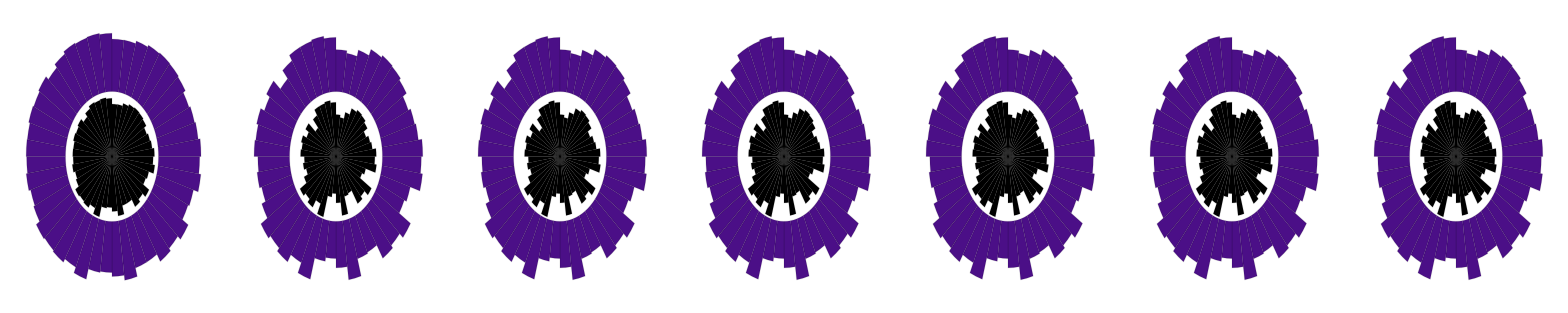

./DARPA_Baseline_Det/evolutionGrid.pdf

```mathematica
data=(dataSets//Transpose);
sectorPlotsA=ParallelTable[
timeStep=data[[i]];
SectorChart[Reverse[Transpose[Transpose[{Append[ConstantArray[1,Length[#]],.0001],Append[#,Total[#]]}]&/@timeStep]],
ChartStyle->{Reverse[colors],None},
ChartBaseStyle->EdgeForm[Directive[Thin,Opacity[.1]]],
PolarGridLines->{None(*Range[0,2Pi,2π/Length[timeStep]]*),None(*Range[0,10,0.5]*)},
GridLinesStyle->Directive[Gray,Opacity[.1],Thin],
PolarAxes->False(*{True,False}*),
PolarTicks->None,
AxesStyle->None(*Directive[Opacity[.1]]*),
PerformanceGoal->"Speed",
SectorOrigin->{{Pi,"Clockwise"},0}
]
,{i,dataRange[[1]],dataRange[[2]],Floor[(dataRange[[2]]-dataRange[[1]])/delta]}];
grid=Grid[{sectorPlotsA}]
Export[dataPath<>"evolutionGrid.pdf",grid,ImageResolution->1000]
```

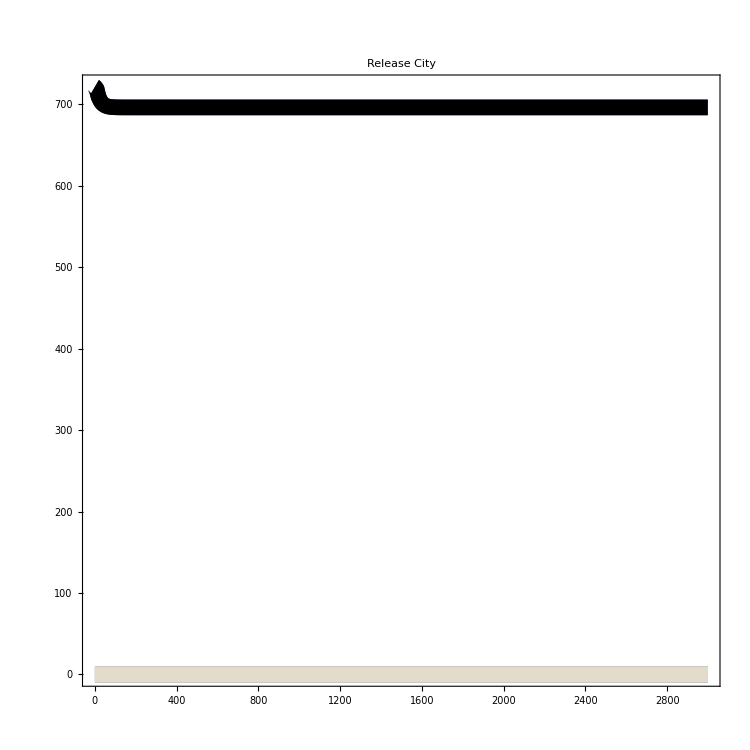
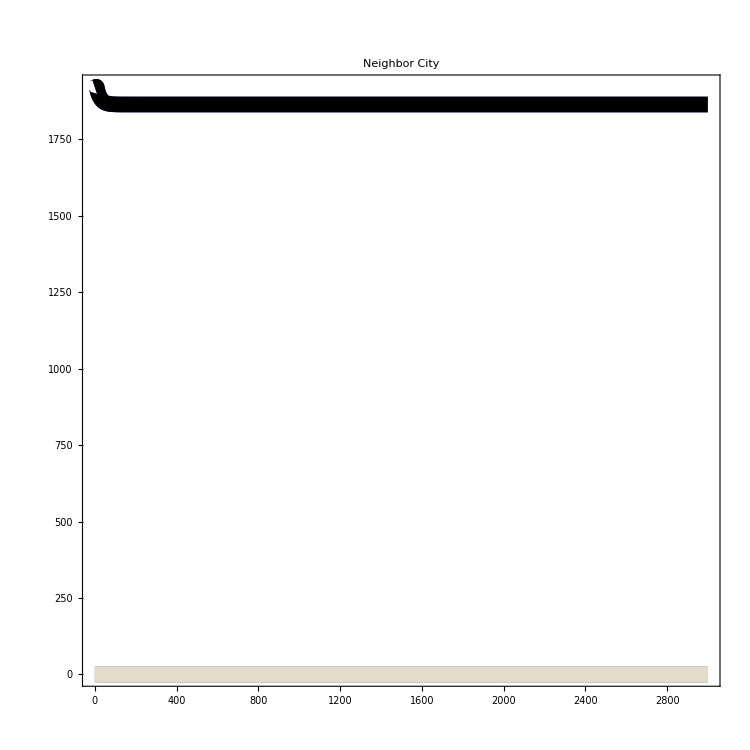
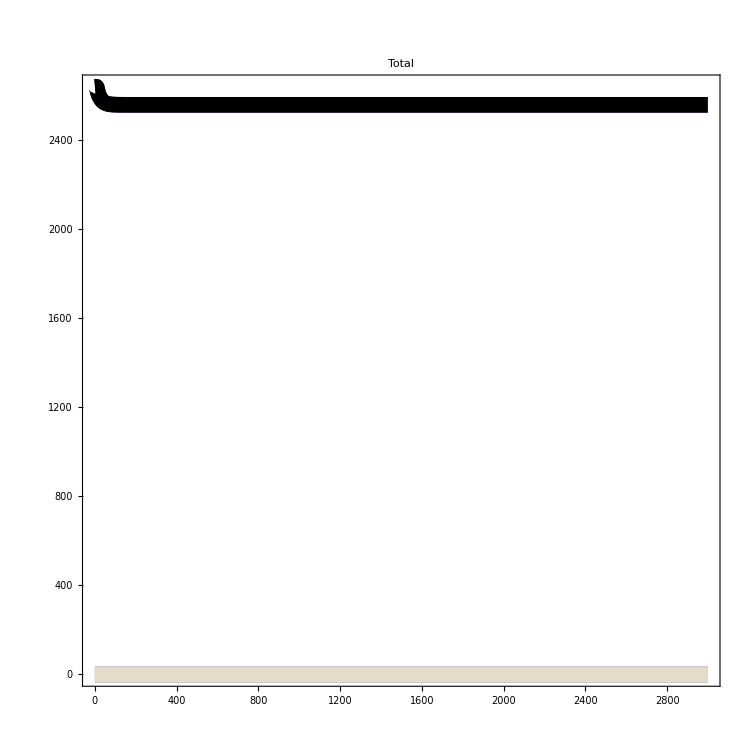
-Graphics- | -Graphics- | -Graphics- |

./DARPA_Baseline_Det/listPlot.png

```mathematica
styles={Thickness[.015],Darker[#,.05]}&/@colors;
listPlot=Grid[{Append[
ListLinePlot[Append[(Transpose/@#[[1]])//Total,(Total[(Transpose/@#[[1]])//Total])],
PlotRange->All,
Frame->True,
FrameStyle->Thick,
PlotStyle->styles,
PlotLabel->Style[#[[2]],35],
ImageSize->750,
AspectRatio->1
]&/@{{dataSets[[33;;44]],"Release City"},{dataSets[[1;;32]],"Neighbor City"},{dataSets[[1;;44]],"Total"}}
,SwatchLegend[colors,Append[genotypes,"Total"],LabelStyle->40,LegendMarkerSize->40]]
}]
Export[dataPath<>"listPlot.png",listPlot,ImageResolution->300]
```

## ListPlot

```mathematica
SetDirectory[NotebookDirectory[]];
popFileNames=FileNames["./DARPA_UDMel_Det/ADF1NoMates_*.csv"];
data=Import[#]&/@popFileNames;
processed=PreProcessPopFiles[#]&/@data;
plotList=ListLinePlot[Append[#[[1]]//Transpose,Total/@(#[[1]])],
PlotRange->{0,80},
AspectRatio->.25,
PlotLegends->None(*processed[[1,2]]*),
Frame->True]&/@processed;
Grid[Partition[plotList,11]//Transpose]
```

```mathematica
SetDirectory[NotebookDirectory[]];
popFileNames=FileNames["./DARPA_TransRem_Det/ADF1NoMates_*.csv"];
data=Import[#]&/@popFileNames;
processed=PreProcessPopFiles[#]&/@data;
plots=MatrixPlotPopulationHistory[#[[1]],#[[2]],{0,1000}]&/@processed;
Grid[{plots}//Transpose];
```

## Functions

```mathematica
GenerateCityFrame[genoBreakdown_,maxPop_]:=ArrayPlot[
{
ConstantArray[genoBreakdown//Total,genoBreakdown//Length],
genoBreakdown
}//Transpose,
ColorFunctionScaling->False,
ColorFunction->(ColorData["LakeColors",Rescale[#1,{0,maxPop},{0,1}]]&),
Frame->None,
ImagePadding->0,
ImageMargins->0,
AspectRatio->1
]
GenerateCityHistoryPlot[genoBreakdownHistory_,maxPop_]:=Grid[{GenerateCityFrame[#,maxPop]&/@genoBreakdownHistory},Spacings->{.1,-1}]
MatrixPlotPopulationHistory[genoHistoryPop_,genotypes_,colorRange_]:=Module[{ticksLabels},
ticksLabels={#[[1]],#[[2]]}&/@({Range[genotypes//Length],genotypes}//Transpose);
MatrixPlot[
genoHistoryPop//Transpose,
(*ColorFunction->ColorData[{"LakeColors",Automatic}],*)
ColorFunction->ColorData["LakeColors"],
(*PlotLegends->Placed[Automatic,Below],*)
ImageSize->750,
PlotRangePadding->0,
Mesh->{Range[9],Range[900,25]},
AspectRatio->.05,
Frame->True,
FrameStyle->Directive[{Opacity[1],Black,5}],
FrameTicks->{{ticksLabels,None},{None,Automatic}}
]
]
PreProcessPopFiles[rawData_]:=Module[{genotypes,genoHistoryPop},
genotypes=rawData[[1]][[2;;(Length[rawData[[1]]-1])]];
genoHistoryPop=rawData[[2;;All]][[All,2;;(Length[rawData[[1]]-1])]];
{genoHistoryPop,genotypes}
]
```

## Grid

## One Frame

```mathematica
genotypesNumber=4;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/genotypesNumber],Black}//Flatten
```

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.49621975, 0.41002485, 0.8144772499999999],RGBColor[0.663226, 0.6872815, 0.9117649999999999],RGBColor[0.80726725, 0.861883, 0.894034],RGBColor[0.941176, 0.906538, 0.834043],GrayLevel[0]}

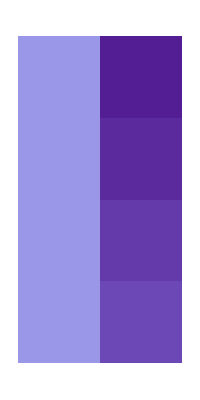

```mathematica
genoBreakdown={1,2,3,4};
maxPop=25;
citiesNumber=10;
GenerateCityFrame[genoBreakdown,maxPop]
```

## Full City History

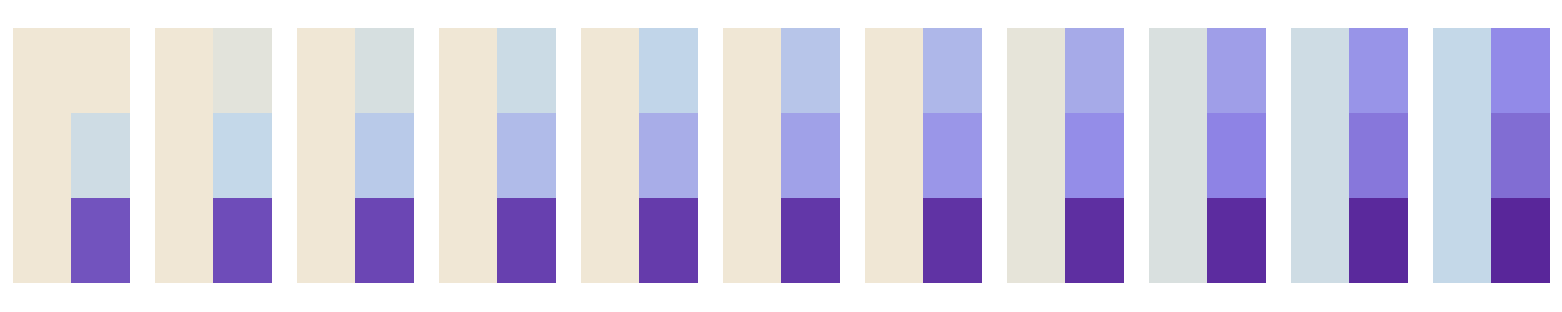

```mathematica
{maxPop,iterations}={100,10};
genoBreakdownHistory=NestList[#*RandomReal[]&,{100,75,19},iterations];
GenerateCityHistoryPlot[genoBreakdownHistory,maxPop]
```

## Full Population History

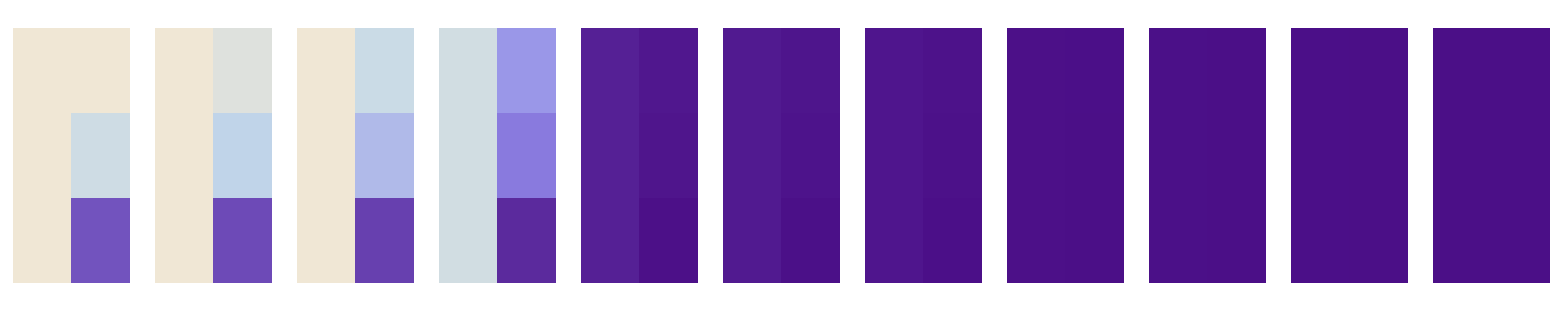
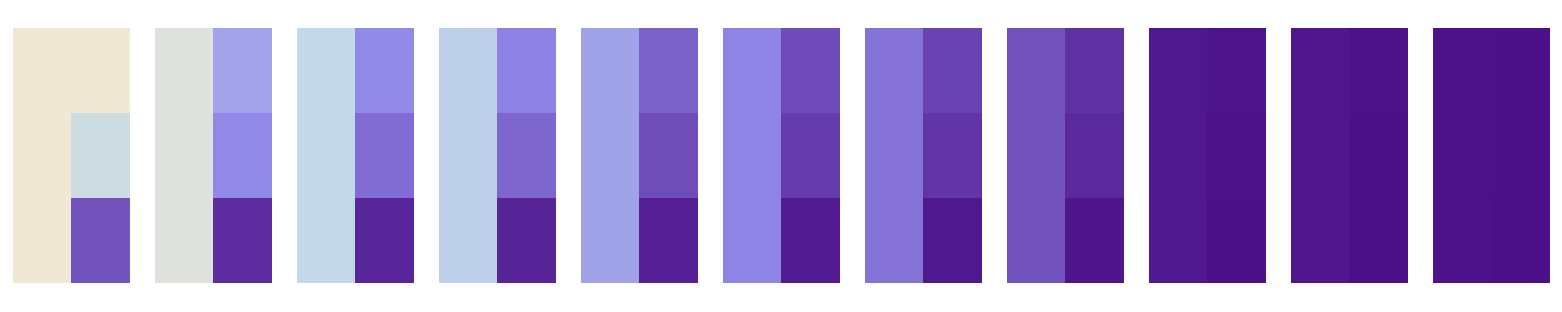
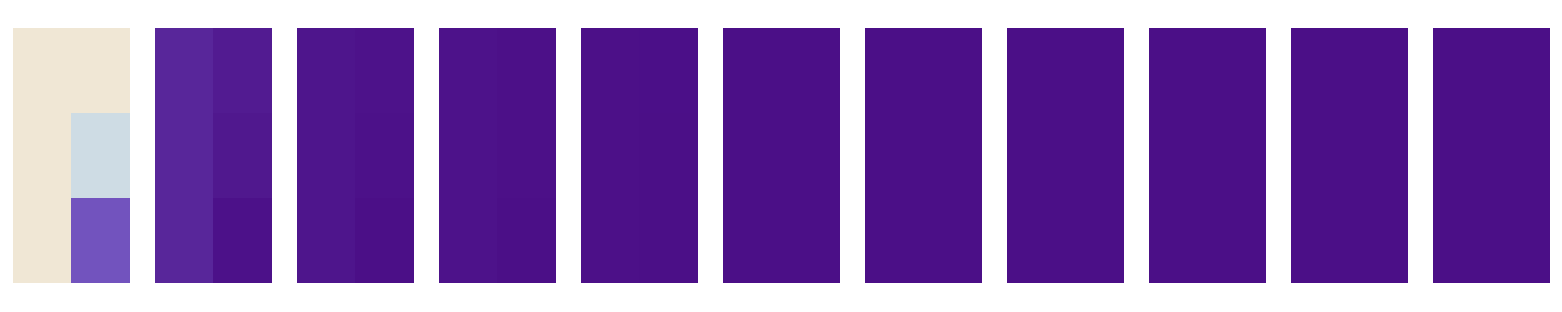
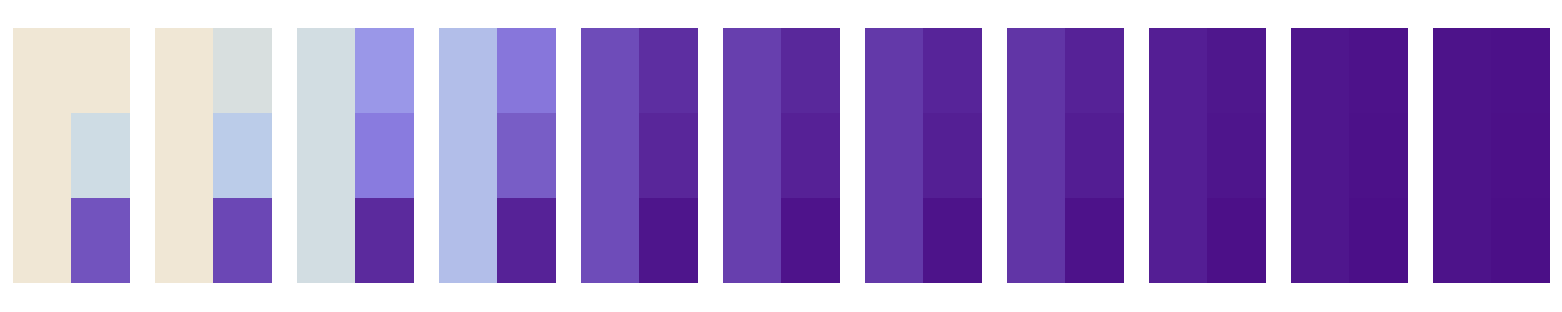
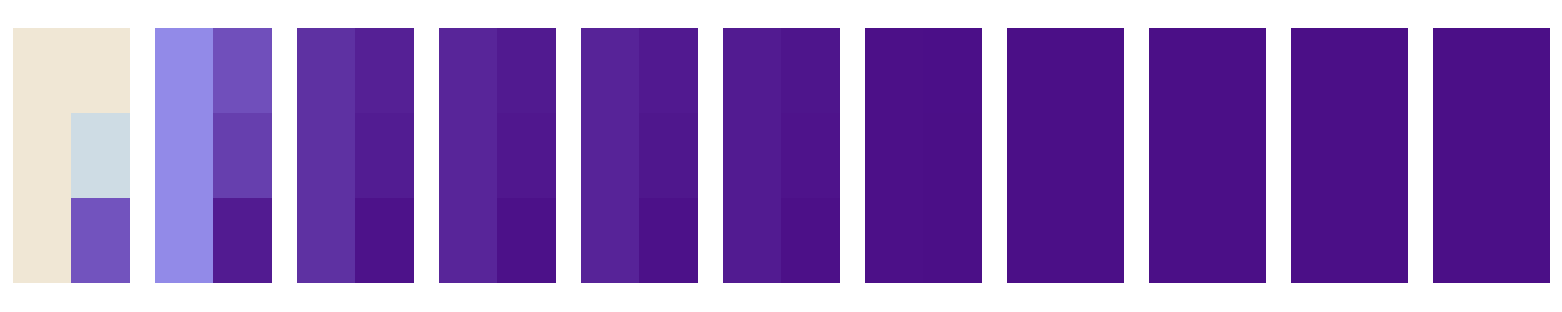
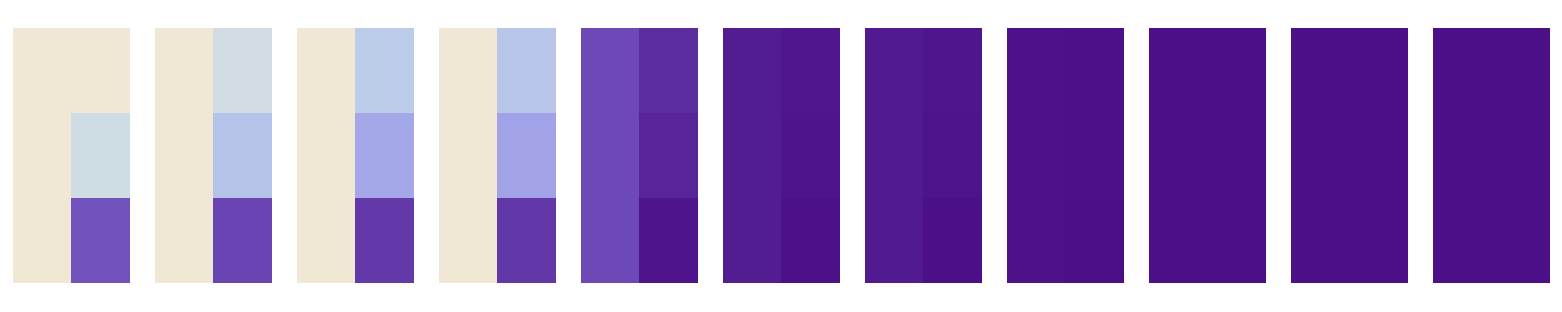
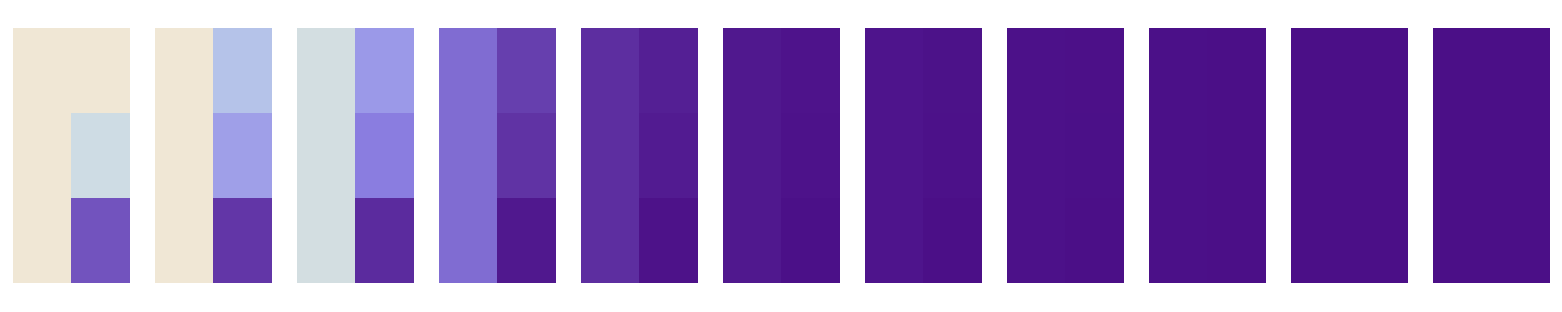
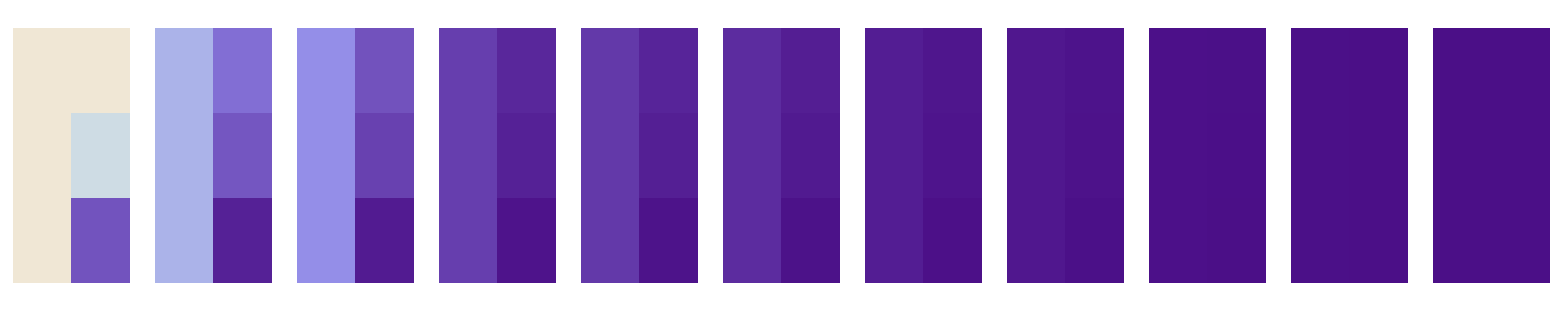

```mathematica
{maxPop,iterations}={100,10};
genoBreakdownHistoryPop=Table[NestList[#*RandomReal[]&,{100,75,19},iterations],{i,1,100}];
Grid[
{GenerateCityHistoryPlot[#,maxPop]}&/@genoBreakdownHistoryPop,
Spacings->{.1,.1}
]
```

## Network Analysis

```mathematica
coords=Import["./accumulateCityDARPA.csv"][[All,{3,2}]];
trans=Import["./accumulateCityDARPA_exponentialKernel.csv"][[2;;All]];
{centroids,pointsNumber,clusteringMethod}={{{-700,-25},{50,50}},20,"DBSCAN"};
{imageSize,imagePadding,plotRange}={1000,50,{{-450,450},{0,0.0035}}};
(**)
range=Range[coords//Length];
eucledianDistances=CalculateEuclideanDistances[coords];
distances=eucledianDistances;
popSizes=Total/@dataSets[[All,500]];
```

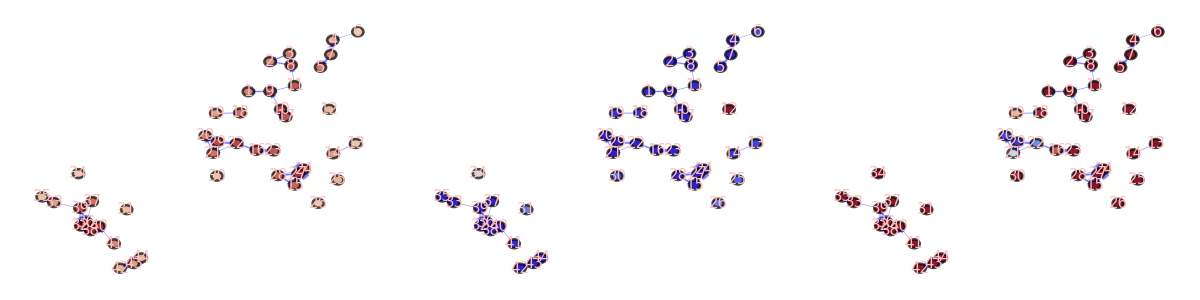

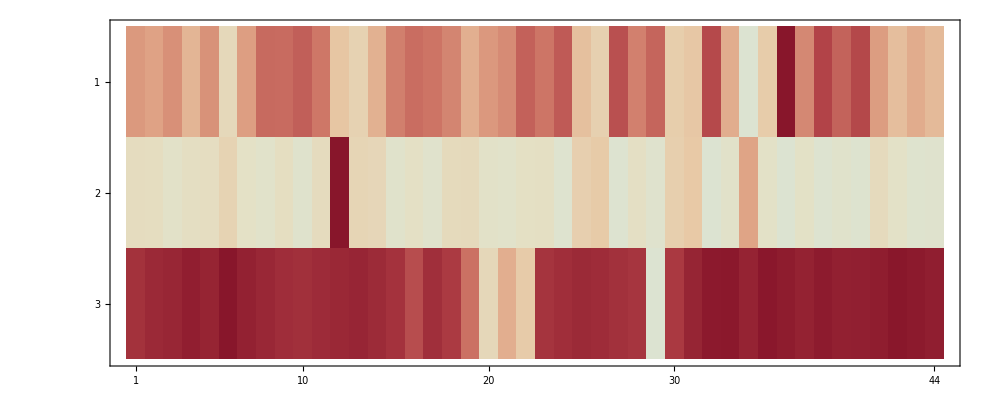

```mathematica
transitions=ReplaceAll[trans,ComplexInfinity->0];
(*transitions=Chop[Quiet[1/distances]//ReplacePart[#,{i_,i_}->0]&,.004];*)
graph=GraphTransitionsFrequenciesWithMax[
{
transitions,
ToString/@Range[Length[coords]]
},.0001
];
graph2=GraphTransitionsFrequenciesWithMax[
{
Chop[transitions//LowerTriangularize,.004]//ReplacePart[#,{i_,i_}->0]&,
ToString/@Range[Length[coords]]
},.0001,
VertexCoordinates->coords,
LineThickness->.00001,
ImageSize->750,
VertexStyle->Directive[Lighter[Red,0.75],EdgeForm[Directive[Thickness[.0025],Black]]],
VertexLabelStyle->Directive[15],
VariableStyle->"LineWidth",
VertexSize->1.5
];
cc=popSizes;
a=HighlightGraph[graph2,Table[Style[VertexList[graph2]⟦i⟧,ColorData["ThermometerColors"][cc⟦i⟧/Max[cc]]],{i,VertexCount[graph]}],ImageSize->750];
cc2=ClosenessCentrality[graph];
b=HighlightGraph[graph2,Table[Style[VertexList[graph2]⟦i⟧,ColorData["ThermometerColors"][cc2⟦i⟧/Max[cc2]]],{i,VertexCount[graph]}],ImageSize->750];
rescaledPopulations=Rescale[popSizes]/Total[Rescale[popSizes]];
markov=DiscreteMarkovProcess[rescaledPopulations,trans];
holdingTime=MarkovProcessProperties[markov,"HoldingTimeMean"];
c=HighlightGraph[graph2,Table[Style[VertexList[graph2]⟦i⟧,ColorData["ThermometerColors"][holdingTime⟦i⟧/Max[holdingTime]]],{i,VertexCount[graph]}],ImageSize->750];
Grid[{{a,c,b}}]
MatrixPlot[{
Rescale[popSizes,{popSizes//Min,popSizes//Max},{0,1}],
Rescale[holdingTime,{holdingTime//Min,holdingTime//Max},{0,1}],
Rescale[cc2,{cc2//Min,cc2//Max},{0,1}]
},ImageSize->1000,ColorFunction->"ThermometerColors"]
```

```mathematica
Rescale[popSizes,{popSizes//Min,popSizes//Max},{0,1}]
Rescale[holdingTime,{holdingTime//Min,holdingTime//Max},{0,1}]
```

{0.480361,0.434751,0.522883,0.312243,0.517693,0.0358624,0.45698,0.7074,0.704778,0.751119,0.659479,0.185462,0.0897194,0.34531,0.606246,0.698119,0.665935,0.576524,0.350648,0.481603,0.547397,0.741739,0.664356,0.776259,0.235382,0.110156,0.839091,0.604902,0.73141,0.128576,0.177884,0.870017,0.358724,0.,0.147545,1.,0.568077,0.895811,0.741202,0.87489,0.460806,0.241174,0.359505,0.276838}

{0.0216896,0.0138572,0.00481049,0.012101,0.0134282,0.0840024,0.00723958,0.00421143,0.0133634,0.002167,0.025749,1.,0.0686589,0.0486652,0.00388014,0.0076634,0.00235623,0.0302733,0.0350956,0.00511127,0.0047347,0.00831636,0.0104098,0.000878054,0.118154,0.152075,0.000530955,0.00885793,0.00215733,0.118784,0.168413,0.000158596,0.0047375,0.424403,0.00520925,0.,0.00580466,0.000219464,0.00329699,0.000769415,0.0266364,0.00537841,0.00128122,0.00207849}